```mathematica
k = 12;
h = 0.16;

df[x_] := -k*x
f[0.0] = 1;
f[t_] := f[t-h] + df[f[t-h]]*h

g[0.0] = 1;
g[t_] := g[t-h] / (1 + h*k)

Slider[Dynamic[k], {0, 50}]
Slider[Dynamic[h], {0.05, 1}]

Dynamic[Show[Plot[E^(-k*t), {t, 0, 1}, PlotRange->{-1, 1}], DiscretePlot[{f[t], g[t]}, {t, 0, 1, h}, Joined->True, PlotRange->{-1, 1}]]]
```

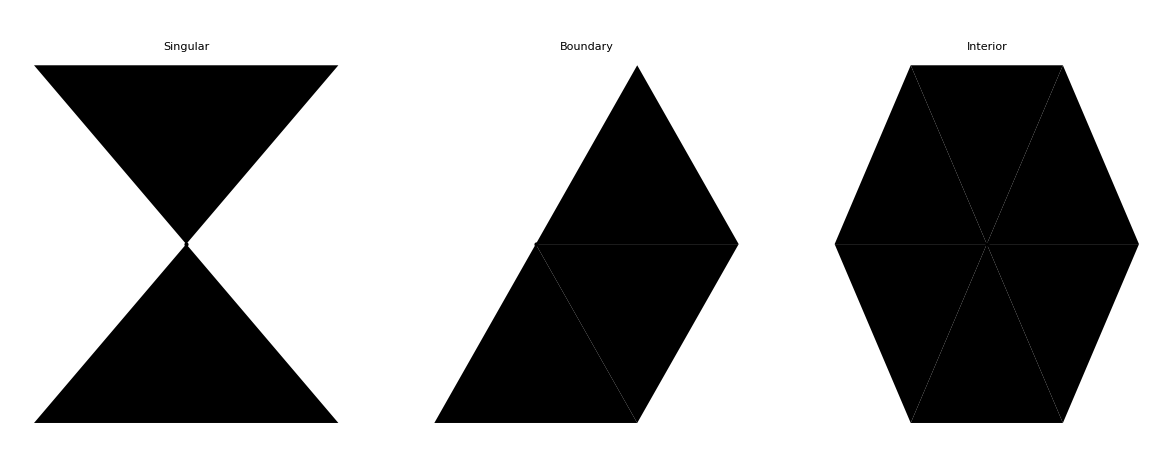

/Users/miles/Kiln/projects/fem/Figures.pdf

```mathematica
apex = {1/2, Sqrt[3]/2};
tri = {{0,0}, {1,0}, apex};
style = {FaceForm[None],EdgeForm[Blue],AbsolutePointSize[8]};

fig = GraphicsRow[{
Graphics[{Polygon[tri], Rotate[Polygon[tri], 180Degree, apex],Point[apex]},PlotLabel->"Singular", BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex], Point[apex]},PlotLabel->"Boundary",BaseStyle->style],

Graphics[{
Rotate[Polygon[tri],0Degree],
Rotate[Polygon[tri],60Degree, apex],
Rotate[Polygon[tri],120Degree, apex],
Rotate[Polygon[tri],180Degree, apex],
Rotate[Polygon[tri],240Degree, apex],
Rotate[Polygon[tri],300Degree, apex] ,Point[apex]},PlotLabel->"Interior", BaseStyle->style]}]

Export[FileNameJoin[{NotebookDirectory[], "figures.pdf"}],fig]
```

{{0.,20.},{-20.,-20.},{-15.2695,-4.58152}}

{{0.72,0.16},{0.72,0.08},{1.2,0.16}}

{{0.48,0.08},{0.4,0.08},{0.96,0.12}}

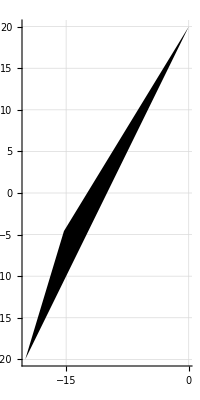

```mathematica
tri1 = {{0.000000,20.000000},{-20.000000,-20.000000},{-15.269472,-4.581519}}
tri2 = {{0.720000,0.160000},{0.720000,0.080000},{1.200000,0.160000}}
tri3 = {{0.480000,0.080000}, {0.400000,0.080000}, {0.960000,0.120000}}
Graphics[{Polygon[tri1]},Axes->True, GridLines->True]
```

```mathematica
tris={{{-2.000000,6.000000},{0.206468,0.857112},{0.524247,0.911537}},{{0.908635,0.182729},{6.000000,-2.000000},{0.927356,0.215003}},{{-2.000000,6.000000},{-2.000000,-2.000000},{0.106179,0.712747}},{{0.206468,0.857112},{-2.000000,6.000000},{0.106179,0.712747}},{{0.935144,0.252052},{6.000000,-2.000000},{0.787099,0.535118}},{{6.000000,-2.000000},{0.554599,0.880127},{0.787099,0.535118}},{{-2.000000,-2.000000},{0.611417,0.082081},{0.525966,0.082040}},{{0.106179,0.712747},{-2.000000,-2.000000},{0.092263,0.537788}},{{6.000000,-2.000000},{0.935144,0.252052},{0.934962,0.242008}},{{0.908635,0.182729},{0.927356,0.215003},{0.879918,0.307200}},{{0.927356,0.215003},{0.931222,0.233540},{0.879918,0.307200}},{{0.935144,0.252052},{0.855050,0.368774},{0.879918,0.307200}},{{0.931222,0.233540},{0.935144,0.252052},{0.879918,0.307200}},{{0.855050,0.368774},{0.771807,0.127611},{0.879918,0.307200}},{{0.524247,0.911537},{0.206468,0.857112},{0.288144,0.864731}},{{6.000000,-2.000000},{-2.000000,6.000000},{0.536897,0.900908}},{{0.554599,0.880127},{6.000000,-2.000000},{0.536897,0.900908}},{{-2.000000,6.000000},{0.524247,0.911537},{0.536897,0.900908}},{{0.524247,0.911537},{0.543224,0.888328},{0.536897,0.900908}},{{0.543224,0.888328},{0.554599,0.880127},{0.536897,0.900908}},{{0.561910,0.860905},{0.554599,0.880127},{0.551337,0.867679}},{{0.554599,0.880127},{0.543224,0.888328},{0.551337,0.867679}},{{0.543224,0.888328},{0.524247,0.911537},{0.453749,0.880196}},{{0.524247,0.911537},{0.288144,0.864731},{0.453749,0.880196}},{{0.288144,0.864731},{0.397748,0.850172},{0.453749,0.880196}},{{0.535654,0.779215},{0.551337,0.867679},{0.453749,0.880196}},{{0.551337,0.867679},{0.543224,0.888328},{0.453749,0.880196}},{{0.699004,0.601992},{0.561611,0.801436},{0.652846,0.619954}},{{0.561611,0.801436},{0.535654,0.779215},{0.652846,0.619954}},{{0.715957,0.590472},{0.699004,0.601992},{0.652846,0.619954}},{{0.528855,0.602676},{0.715957,0.590472},{0.652846,0.619954}},{{0.535654,0.779215},{0.528855,0.602676},{0.652846,0.619954}},{{0.561611,0.801436},{0.699004,0.601992},{0.564541,0.826528}},{{0.535654,0.779215},{0.561611,0.801436},{0.564541,0.826528}},{{0.551337,0.867679},{0.535654,0.779215},{0.564541,0.826528}},{{0.561910,0.860905},{0.551337,0.867679},{0.564541,0.826528}},{{0.855050,0.368774},{0.935144,0.252052},{0.844631,0.415413}},{{0.935144,0.252052},{0.787099,0.535118},{0.844631,0.415413}},{{0.736391,0.579902},{0.715957,0.590472},{0.785573,0.524318}},{{0.715957,0.590472},{0.528855,0.602676},{0.785573,0.524318}},{{0.844631,0.415413},{0.787099,0.535118},{0.785573,0.524318}},{{0.561910,0.860905},{0.736391,0.579902},{0.773103,0.553917}},{{0.554599,0.880127},{0.561910,0.860905},{0.773103,0.553917}},{{0.787099,0.535118},{0.554599,0.880127},{0.773103,0.553917}},{{0.736391,0.579902},{0.785573,0.524318},{0.773103,0.553917}},{{0.785573,0.524318},{0.787099,0.535118},{0.773103,0.553917}},{{0.699004,0.601992},{0.715957,0.590472},{0.703640,0.600086}},{{0.715957,0.590472},{0.719385,0.589508},{0.703640,0.600086}},{{0.736391,0.579902},{0.561910,0.860905},{0.703640,0.600086}},{{0.719385,0.589508},{0.736391,0.579902},{0.703640,0.600086}},{{0.564541,0.826528},{0.699004,0.601992},{0.703640,0.600086}},{{0.561910,0.860905},{0.564541,0.826528},{0.703640,0.600086}},{{0.528855,0.602676},{0.499940,0.594147},{0.580866,0.089681}},{{0.525966,0.082040},{0.611417,0.082081},{0.580866,0.089681}},{{0.855050,0.368774},{0.844631,0.415413},{0.580866,0.089681}},{{0.844631,0.415413},{0.785573,0.524318},{0.580866,0.089681}},{{0.785573,0.524318},{0.528855,0.602676},{0.580866,0.089681}},{{0.256632,0.223429},{0.445704,0.587407},{0.422100,0.590173}},{{0.445704,0.587407},{0.402814,0.602508},{0.422100,0.590173}},{{0.210417,0.253601},{0.256632,0.223429},{0.422100,0.590173}},{{0.169779,0.293888},{0.210417,0.253601},{0.422100,0.590173}},{{0.138640,0.347481},{0.169779,0.293888},{0.422100,0.590173}},{{0.499940,0.594147},{0.528855,0.602676},{0.512420,0.602980}},{{0.445704,0.587407},{0.499940,0.594147},{0.512420,0.602980}},{{0.455022,0.735625},{0.445704,0.587407},{0.512420,0.602980}},{{0.528855,0.602676},{0.535654,0.779215},{0.495778,0.755385}},{{0.397748,0.850172},{0.455022,0.735625},{0.495778,0.755385}},{{0.453749,0.880196},{0.397748,0.850172},{0.495778,0.755385}},{{0.535654,0.779215},{0.453749,0.880196},{0.495778,0.755385}},{{0.455022,0.735625},{0.512420,0.602980},{0.495778,0.755385}},{{0.512420,0.602980},{0.528855,0.602676},{0.495778,0.755385}},{{0.402814,0.602508},{0.445704,0.587407},{0.418175,0.721326}},{{0.445704,0.587407},{0.455022,0.735625},{0.418175,0.721326}},{{0.201861,0.751229},{0.402814,0.602508},{0.418175,0.721326}},{{0.455022,0.735625},{0.397748,0.850172},{0.418175,0.721326}},{{0.397748,0.850172},{0.288144,0.864731},{0.418175,0.721326}},{{0.288144,0.864731},{0.201861,0.751229},{0.418175,0.721326}},{{-2.000000,-2.000000},{6.000000,-2.000000},{0.667843,0.086259}},{{0.611417,0.082081},{-2.000000,-2.000000},{0.667843,0.086259}},{{0.580866,0.089681},{0.611417,0.082081},{0.667843,0.086259}},{{0.771807,0.127611},{0.855050,0.368774},{0.667843,0.086259}},{{0.855050,0.368774},{0.580866,0.089681},{0.667843,0.086259}},{{6.000000,-2.000000},{0.908635,0.182729},{0.860036,0.146894}},{{0.908635,0.182729},{0.879918,0.307200},{0.860036,0.146894}},{{0.879918,0.307200},{0.771807,0.127611},{0.860036,0.146894}},{{0.771807,0.127611},{0.667843,0.086259},{0.860036,0.146894}},{{0.667843,0.086259},{6.000000,-2.000000},{0.860036,0.146894}},{{0.499940,0.594147},{0.445704,0.587407},{0.472370,0.087084}},{{0.445848,0.086396},{0.525966,0.082040},{0.472370,0.087084}},{{0.525966,0.082040},{0.580866,0.089681},{0.472370,0.087084}},{{0.580866,0.089681},{0.499940,0.594147},{0.472370,0.087084}},{{0.277880,0.087678},{-2.000000,-2.000000},{0.320154,0.087609}},{{-2.000000,-2.000000},{0.362238,0.087367},{0.320154,0.087609}},{{0.445848,0.086396},{0.472370,0.087084},{0.296752,0.186266}},{{0.445704,0.587407},{0.256632,0.223429},{0.296752,0.186266}},{{0.472370,0.087084},{0.445704,0.587407},{0.296752,0.186266}},{{0.277880,0.087678},{0.320154,0.087609},{0.296752,0.186266}},{{0.320154,0.087609},{0.362238,0.087367},{0.296752,0.186266}},{{-2.000000,-2.000000},{0.525966,0.082040},{0.432528,0.085577}},{{0.362238,0.087367},{-2.000000,-2.000000},{0.432528,0.085577}},{{0.525966,0.082040},{0.445848,0.086396},{0.432528,0.085577}},{{0.445848,0.086396},{0.296752,0.186266},{0.432528,0.085577}},{{0.296752,0.186266},{0.362238,0.087367},{0.432528,0.085577}},{{0.092263,0.537788},{0.119153,0.412324},{0.137163,0.488550}},{{0.422100,0.590173},{0.402814,0.602508},{0.137163,0.488550}},{{0.119153,0.412324},{0.138640,0.347481},{0.137163,0.488550}},{{0.138640,0.347481},{0.422100,0.590173},{0.137163,0.488550}},{{0.206468,0.857112},{0.106179,0.712747},{0.191862,0.792693}},{{0.106179,0.712747},{0.201861,0.751229},{0.191862,0.792693}},{{0.201861,0.751229},{0.288144,0.864731},{0.191862,0.792693}},{{0.288144,0.864731},{0.206468,0.857112},{0.191862,0.792693}},{{0.106179,0.712747},{0.092263,0.537788},{0.115497,0.645241}},{{0.201861,0.751229},{0.106179,0.712747},{0.115497,0.645241}},{{0.402814,0.602508},{0.201861,0.751229},{0.115497,0.645241}},{{0.137163,0.488550},{0.402814,0.602508},{0.115497,0.645241}},{{0.092263,0.537788},{0.137163,0.488550},{0.115497,0.645241}},{{-2.000000,-2.000000},{0.277880,0.087678},{0.235057,0.132196}},{{0.256632,0.223429},{0.210417,0.253601},{0.235057,0.132196}},{{0.210417,0.253601},{0.169779,0.293888},{0.235057,0.132196}},{{0.169779,0.293888},{0.138640,0.347481},{0.235057,0.132196}},{{0.138640,0.347481},{-2.000000,-2.000000},{0.235057,0.132196}},{{0.277880,0.087678},{0.296752,0.186266},{0.235057,0.132196}},{{0.296752,0.186266},{0.256632,0.223429},{0.235057,0.132196}},{{0.119153,0.412324},{0.092263,0.537788},{0.125137,0.375700}},{{0.092263,0.537788},{-2.000000,-2.000000},{0.125137,0.375700}},{{-2.000000,-2.000000},{0.138640,0.347481},{0.125137,0.375700}},{{0.138640,0.347481},{0.119153,0.412324},{0.125137,0.375700}},{{0.927356,0.215003},{6.000000,-2.000000},{0.932931,0.227727}},{{6.000000,-2.000000},{0.934962,0.242008},{0.932931,0.227727}},{{0.934962,0.242008},{0.927356,0.215003},{0.932931,0.227727}}}
pr={0.916187,0.204013}
edges={{{0.908635,0.182729},{0.927356,0.215003}},{{0.927356,0.215003},{0.931222,0.233540}},{{0.931222,0.233540},{0.879918,0.307200}},{{0.879918,0.307200},{0.860036,0.146894}},{{0.860036,0.146894},{0.908635,0.182729}},{{0.934962,0.242008},{0.927356,0.215003}},{{0.927356,0.215003},{0.932931,0.227727}},{{0.932931,0.227727},{0.934962,0.242008}}}


Graphics[{FaceForm[Black],EdgeForm[Blue], Polygon/@tris, Pink, Point[pr]}]
Graphics[{FaceForm[None],EdgeForm[Blue], Line/@edges, Pink, Point[pr]}]
```

{{{-2.,6.},{0.206468,0.857112},{0.524247,0.911537}},{{0.908635,0.182729},{6.,-2.},{0.927356,0.215003}},{{-2.,6.},{-2.,-2.},{0.106179,0.712747}},{{0.206468,0.857112},{-2.,6.},{0.106179,0.712747}},{{0.935144,0.252052},{6.,-2.},{0.787099,0.535118}},{{6.,-2.},{0.554599,0.880127},{0.787099,0.535118}},{{-2.,-2.},{0.611417,0.082081},{0.525966,0.08204}},{{0.106179,0.712747},{-2.,-2.},{0.092263,0.537788}},{{6.,-2.},{0.935144,0.252052},{0.934962,0.242008}},{{0.908635,0.182729},{0.927356,0.215003},{0.879918,0.3072}},{{0.927356,0.215003},{0.931222,0.23354},{0.879918,0.3072}},{{0.935144,0.252052},{0.85505,0.368774},{0.879918,0.3072}},{{0.931222,0.23354},{0.935144,0.252052},{0.879918,0.3072}},{{0.85505,0.368774},{0.771807,0.127611},{0.879918,0.3072}},{{0.524247,0.911537},{0.206468,0.857112},{0.288144,0.864731}},{{6.,-2.},{-2.,6.},{0.536897,0.900908}},{{0.554599,0.880127},{6.,-2.},{0.536897,0.900908}},{{-2.,6.},{0.524247,0.911537},{0.536897,0.900908}},{{0.524247,0.911537},{0.543224,0.888328},{0.536897,0.900908}},{{0.543224,0.888328},{0.554599,0.880127},{0.536897,0.900908}},{{0.56191,0.860905},{0.554599,0.880127},{0.551337,0.867679}},{{0.554599,0.880127},{0.543224,0.888328},{0.551337,0.867679}},{{0.543224,0.888328},{0.524247,0.911537},{0.453749,0.880196}},{{0.524247,0.911537},{0.288144,0.864731},{0.453749,0.880196}},{{0.288144,0.864731},{0.397748,0.850172},{0.453749,0.880196}},{{0.535654,0.779215},{0.551337,0.867679},{0.453749,0.880196}},{{0.551337,0.867679},{0.543224,0.888328},{0.453749,0.880196}},{{0.699004,0.601992},{0.561611,0.801436},{0.652846,0.619954}},{{0.561611,0.801436},{0.535654,0.779215},{0.652846,0.619954}},{{0.715957,0.590472},{0.699004,0.601992},{0.652846,0.619954}},{{0.528855,0.602676},{0.715957,0.590472},{0.652846,0.619954}},{{0.535654,0.779215},{0.528855,0.602676},{0.652846,0.619954}},{{0.561611,0.801436},{0.699004,0.601992},{0.564541,0.826528}},{{0.535654,0.779215},{0.561611,0.801436},{0.564541,0.826528}},{{0.551337,0.867679},{0.535654,0.779215},{0.564541,0.826528}},{{0.56191,0.860905},{0.551337,0.867679},{0.564541,0.826528}},{{0.85505,0.368774},{0.935144,0.252052},{0.844631,0.415413}},{{0.935144,0.252052},{0.787099,0.535118},{0.844631,0.415413}},{{0.736391,0.579902},{0.715957,0.590472},{0.785573,0.524318}},{{0.715957,0.590472},{0.528855,0.602676},{0.785573,0.524318}},{{0.844631,0.415413},{0.787099,0.535118},{0.785573,0.524318}},{{0.56191,0.860905},{0.736391,0.579902},{0.773103,0.553917}},{{0.554599,0.880127},{0.56191,0.860905},{0.773103,0.553917}},{{0.787099,0.535118},{0.554599,0.880127},{0.773103,0.553917}},{{0.736391,0.579902},{0.785573,0.524318},{0.773103,0.553917}},{{0.785573,0.524318},{0.787099,0.535118},{0.773103,0.553917}},{{0.699004,0.601992},{0.715957,0.590472},{0.70364,0.600086}},{{0.715957,0.590472},{0.719385,0.589508},{0.70364,0.600086}},{{0.736391,0.579902},{0.56191,0.860905},{0.70364,0.600086}},{{0.719385,0.589508},{0.736391,0.579902},{0.70364,0.600086}},{{0.564541,0.826528},{0.699004,0.601992},{0.70364,0.600086}},{{0.56191,0.860905},{0.564541,0.826528},{0.70364,0.600086}},{{0.528855,0.602676},{0.49994,0.594147},{0.580866,0.089681}},{{0.525966,0.08204},{0.611417,0.082081},{0.580866,0.089681}},{{0.85505,0.368774},{0.844631,0.415413},{0.580866,0.089681}},{{0.844631,0.415413},{0.785573,0.524318},{0.580866,0.089681}},{{0.785573,0.524318},{0.528855,0.602676},{0.580866,0.089681}},{{0.256632,0.223429},{0.445704,0.587407},{0.4221,0.590173}},{{0.445704,0.587407},{0.402814,0.602508},{0.4221,0.590173}},{{0.210417,0.253601},{0.256632,0.223429},{0.4221,0.590173}},{{0.169779,0.293888},{0.210417,0.253601},{0.4221,0.590173}},{{0.13864,0.347481},{0.169779,0.293888},{0.4221,0.590173}},{{0.49994,0.594147},{0.528855,0.602676},{0.51242,0.60298}},{{0.445704,0.587407},{0.49994,0.594147},{0.51242,0.60298}},{{0.455022,0.735625},{0.445704,0.587407},{0.51242,0.60298}},{{0.528855,0.602676},{0.535654,0.779215},{0.495778,0.755385}},{{0.397748,0.850172},{0.455022,0.735625},{0.495778,0.755385}},{{0.453749,0.880196},{0.397748,0.850172},{0.495778,0.755385}},{{0.535654,0.779215},{0.453749,0.880196},{0.495778,0.755385}},{{0.455022,0.735625},{0.51242,0.60298},{0.495778,0.755385}},{{0.51242,0.60298},{0.528855,0.602676},{0.495778,0.755385}},{{0.402814,0.602508},{0.445704,0.587407},{0.418175,0.721326}},{{0.445704,0.587407},{0.455022,0.735625},{0.418175,0.721326}},{{0.201861,0.751229},{0.402814,0.602508},{0.418175,0.721326}},{{0.455022,0.735625},{0.397748,0.850172},{0.418175,0.721326}},{{0.397748,0.850172},{0.288144,0.864731},{0.418175,0.721326}},{{0.288144,0.864731},{0.201861,0.751229},{0.418175,0.721326}},{{-2.,-2.},{6.,-2.},{0.667843,0.086259}},{{0.611417,0.082081},{-2.,-2.},{0.667843,0.086259}},{{0.580866,0.089681},{0.611417,0.082081},{0.667843,0.086259}},{{0.771807,0.127611},{0.85505,0.368774},{0.667843,0.086259}},{{0.85505,0.368774},{0.580866,0.089681},{0.667843,0.086259}},{{6.,-2.},{0.908635,0.182729},{0.860036,0.146894}},{{0.908635,0.182729},{0.879918,0.3072},{0.860036,0.146894}},{{0.879918,0.3072},{0.771807,0.127611},{0.860036,0.146894}},{{0.771807,0.127611},{0.667843,0.086259},{0.860036,0.146894}},{{0.667843,0.086259},{6.,-2.},{0.860036,0.146894}},{{0.49994,0.594147},{0.445704,0.587407},{0.47237,0.087084}},{{0.445848,0.086396},{0.525966,0.08204},{0.47237,0.087084}},{{0.525966,0.08204},{0.580866,0.089681},{0.47237,0.087084}},{{0.580866,0.089681},{0.49994,0.594147},{0.47237,0.087084}},{{0.27788,0.087678},{-2.,-2.},{0.320154,0.087609}},{{-2.,-2.},{0.362238,0.087367},{0.320154,0.087609}},{{0.445848,0.086396},{0.47237,0.087084},{0.296752,0.186266}},{{0.445704,0.587407},{0.256632,0.223429},{0.296752,0.186266}},{{0.47237,0.087084},{0.445704,0.587407},{0.296752,0.186266}},{{0.27788,0.087678},{0.320154,0.087609},{0.296752,0.186266}},{{0.320154,0.087609},{0.362238,0.087367},{0.296752,0.186266}},{{-2.,-2.},{0.525966,0.08204},{0.432528,0.085577}},{{0.362238,0.087367},{-2.,-2.},{0.432528,0.085577}},{{0.525966,0.08204},{0.445848,0.086396},{0.432528,0.085577}},{{0.445848,0.086396},{0.296752,0.186266},{0.432528,0.085577}},{{0.296752,0.186266},{0.362238,0.087367},{0.432528,0.085577}},{{0.092263,0.537788},{0.119153,0.412324},{0.137163,0.48855}},{{0.4221,0.590173},{0.402814,0.602508},{0.137163,0.48855}},{{0.119153,0.412324},{0.13864,0.347481},{0.137163,0.48855}},{{0.13864,0.347481},{0.4221,0.590173},{0.137163,0.48855}},{{0.206468,0.857112},{0.106179,0.712747},{0.191862,0.792693}},{{0.106179,0.712747},{0.201861,0.751229},{0.191862,0.792693}},{{0.201861,0.751229},{0.288144,0.864731},{0.191862,0.792693}},{{0.288144,0.864731},{0.206468,0.857112},{0.191862,0.792693}},{{0.106179,0.712747},{0.092263,0.537788},{0.115497,0.645241}},{{0.201861,0.751229},{0.106179,0.712747},{0.115497,0.645241}},{{0.402814,0.602508},{0.201861,0.751229},{0.115497,0.645241}},{{0.137163,0.48855},{0.402814,0.602508},{0.115497,0.645241}},{{0.092263,0.537788},{0.137163,0.48855},{0.115497,0.645241}},{{-2.,-2.},{0.27788,0.087678},{0.235057,0.132196}},{{0.256632,0.223429},{0.210417,0.253601},{0.235057,0.132196}},{{0.210417,0.253601},{0.169779,0.293888},{0.235057,0.132196}},{{0.169779,0.293888},{0.13864,0.347481},{0.235057,0.132196}},{{0.13864,0.347481},{-2.,-2.},{0.235057,0.132196}},{{0.27788,0.087678},{0.296752,0.186266},{0.235057,0.132196}},{{0.296752,0.186266},{0.256632,0.223429},{0.235057,0.132196}},{{0.119153,0.412324},{0.092263,0.537788},{0.125137,0.3757}},{{0.092263,0.537788},{-2.,-2.},{0.125137,0.3757}},{{-2.,-2.},{0.13864,0.347481},{0.125137,0.3757}},{{0.13864,0.347481},{0.119153,0.412324},{0.125137,0.3757}},{{0.927356,0.215003},{6.,-2.},{0.932931,0.227727}},{{6.,-2.},{0.934962,0.242008},{0.932931,0.227727}},{{0.934962,0.242008},{0.927356,0.215003},{0.932931,0.227727}}}

{0.916187,0.204013}

{{{0.908635,0.182729},{0.927356,0.215003}},{{0.927356,0.215003},{0.931222,0.23354}},{{0.931222,0.23354},{0.879918,0.3072}},{{0.879918,0.3072},{0.860036,0.146894}},{{0.860036,0.146894},{0.908635,0.182729}},{{0.934962,0.242008},{0.927356,0.215003}},{{0.927356,0.215003},{0.932931,0.227727}},{{0.932931,0.227727},{0.934962,0.242008}}}

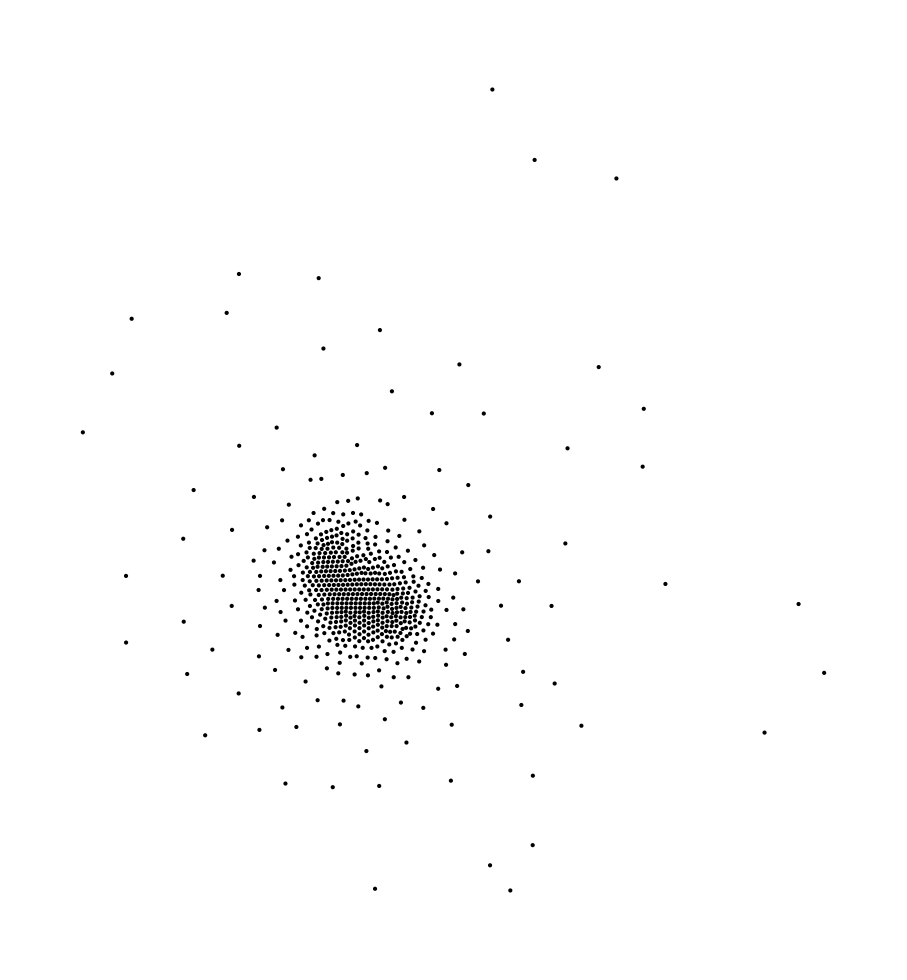

```mathematica
vr={{-0.461034,-0.434969},{0.001739,-0.268200},{0.085672,-0.385228},{-0.135813,-0.402612},{1.368199,-1.366140},{1.246697,-1.215074},{0.020188,-0.724578},{0.557225,-1.355910},{0.582077,-0.738935},{0.303743,-0.746440},{0.346714,-0.369509},{0.505344,-0.529643},{0.616031,-0.338792},{0.595445,-0.141664},{0.745547,-0.478586},{0.712299,-0.238642},{1.503371,-0.677408},{-0.042133,-0.043027},{0.140845,-0.112414},{0.206384,0.036189},{0.268586,-0.033313},{0.212992,-0.224597},{0.368531,-0.227154},{0.336762,-0.063413},{0.456839,-0.261692},{0.434726,-0.069969},{0.477593,-0.004021},{0.514780,-0.075207},{0.581564,-0.045364},{0.558401,0.028567},{0.626476,0.021275},{0.669237,-0.086685},{0.691369,-0.002553},{0.757269,-0.086566},{0.846473,-0.270497},{1.011934,-0.707299},{-0.260276,-0.183950},{0.038172,0.077122},{0.115057,0.033029},{0.271954,0.052423},{0.331561,0.107324},{0.348072,0.061603},{0.345570,-0.000264},{0.408388,0.035706},{0.437419,0.098191},{0.447246,0.038842},{0.483321,0.089714},{0.513055,0.031264},{0.536062,0.089353},{0.571005,0.097852},{0.614888,0.069982},{0.642386,0.110100},{0.668249,0.065522},{0.682730,0.116342},{0.717642,0.089452},{0.746593,0.023805},{0.821850,0.007971},{0.935773,-0.155711},{1.016959,-0.371674},{1.502282,-1.094123},{0.149648,0.089361},{0.220703,0.097216},{0.283577,0.133473},{0.324916,0.143673},{0.364921,0.136179},{0.378630,0.101847},{0.402712,0.137145},{0.436061,0.151703},{0.462817,0.129960},{0.490747,0.148143},{0.515626,0.129017},{0.545066,0.137806},{0.573563,0.153702},{0.602090,0.128793},{0.628268,0.155782},{0.657294,0.152077},{0.692623,0.156022},{0.721096,0.137085},{0.781942,0.079737},{0.802921,0.120234},{0.851156,0.069679},{0.982960,-0.011964},{1.049209,-0.139026},{1.434263,-0.253203},{1.794340,-0.377741},{0.253249,0.177838},{0.307755,0.178103},{0.342373,0.182306},{0.376123,0.187592},{0.401241,0.169328},{0.434873,0.188054},{0.464186,0.171536},{0.491665,0.187555},{0.518012,0.168500},{0.547090,0.182430},{0.572901,0.192956},{0.598478,0.172079},{0.622302,0.190195},{0.647661,0.185915},{0.675330,0.186958},{0.709425,0.178698},{0.747111,0.159451},{0.767198,0.174172},{0.809836,0.172447},{0.860237,0.138443},{0.980138,0.078829},{1.095396,0.052828},{1.444887,-0.054226},{0.122609,0.155314},{0.206808,0.164111},{0.284255,0.209484},{0.320454,0.213687},{0.351141,0.215716},{0.381611,0.222998},{0.406563,0.207388},{0.436628,0.223524},{0.463968,0.207890},{0.492066,0.223552},{0.519552,0.207165},{0.545730,0.216984},{0.574168,0.228023},{0.600263,0.210843},{0.627401,0.219636},{0.656830,0.219947},{0.686510,0.220198},{0.722244,0.202964},{0.743321,0.209337},{0.773594,0.206694},{0.799066,0.217328},{0.847262,0.194077},{0.904842,0.174982},{1.031505,0.140161},{1.113454,0.190836},{2.892210,-0.419001},{-0.138683,0.038703},{0.208040,0.202514},{0.246776,0.219722},{0.290226,0.241359},{0.323212,0.244877},{0.354345,0.248216},{0.382169,0.254244},{0.409928,0.239529},{0.436826,0.253228},{0.464559,0.239988},{0.491829,0.253433},{0.519362,0.238362},{0.547102,0.248316},{0.574184,0.254923},{0.602189,0.240201},{0.631781,0.249348},{0.660565,0.244303},{0.684935,0.252765},{0.711533,0.237868},{0.734866,0.248499},{0.764870,0.242440},{0.796848,0.254224},{0.825601,0.239633},{0.876101,0.231446},{0.930849,0.228326},{1.037722,0.232144},{1.634012,-0.124421},{-0.568940,-0.067325},{0.078977,0.179408},{0.149905,0.218508},{0.215889,0.248361},{0.258672,0.264201},{0.295261,0.271391},{0.327074,0.273799},{0.354824,0.275225},{0.383834,0.282054},{0.409778,0.270840},{0.434025,0.280180},{0.463123,0.272867},{0.492685,0.281694},{0.520041,0.270406},{0.546156,0.275825},{0.575822,0.282879},{0.602856,0.271145},{0.626723,0.278951},{0.654278,0.273531},{0.681967,0.279520},{0.710292,0.272666},{0.738590,0.273971},{0.767035,0.274733},{0.795248,0.282342},{0.837539,0.274202},{0.891527,0.273732},{0.985584,0.316959},{1.354914,0.138066},{1.615229,0.340995},{-0.026679,0.167626},{0.113081,0.252534},{0.179166,0.273041},{0.228169,0.288821},{0.267705,0.295785},{0.299526,0.300245},{0.328806,0.302181},{0.356048,0.303708},{0.381871,0.306794},{0.409277,0.300738},{0.439796,0.303388},{0.465555,0.302623},{0.491347,0.306896},{0.519362,0.300046},{0.547996,0.304107},{0.574129,0.307721},{0.602457,0.299919},{0.634181,0.305307},{0.662200,0.298534},{0.688773,0.302747},{0.716069,0.305050},{0.744692,0.298712},{0.770144,0.305116},{0.803681,0.306385},{0.847813,0.307583},{0.894203,0.318721},{1.086650,0.320764},{1.312518,0.342459},{3.249515,-0.060383},{-0.935174,0.121459},{0.020515,0.252960},{0.151105,0.300833},{0.193779,0.312331},{0.237632,0.321712},{0.272989,0.326117},{0.301401,0.329211},{0.330006,0.329322},{0.357658,0.329504},{0.385180,0.329557},{0.412544,0.329580},{0.439899,0.329601},{0.467243,0.329601},{0.494584,0.329602},{0.522219,0.329688},{0.550072,0.329825},{0.579471,0.332069},{0.608621,0.326611},{0.631848,0.335930},{0.659294,0.323247},{0.685740,0.329434},{0.710867,0.335235},{0.739696,0.328302},{0.774946,0.331524},{0.811826,0.337241},{0.859733,0.344954},{0.936198,0.370765},{-0.132292,0.220453},{0.095326,0.320955},{0.166861,0.340749},{0.214233,0.350255},{0.247994,0.349795},{0.274666,0.356313},{0.302993,0.356778},{0.331509,0.356567},{0.359034,0.356622},{0.386497,0.356646},{0.413849,0.356671},{0.441190,0.356689},{0.468531,0.356708},{0.495869,0.356724},{0.523118,0.356582},{0.549909,0.356767},{0.573500,0.360766},{0.600904,0.354843},{0.627188,0.361866},{0.656611,0.352978},{0.686544,0.357266},{0.719555,0.361353},{0.748794,0.354279},{0.779492,0.363157},{0.819104,0.367317},{0.878845,0.394387},{1.026004,0.390870},{-0.418048,0.078930},{-0.103292,0.330572},{-0.009009,0.304376},{0.141141,0.377785},{0.197500,0.376793},{0.238956,0.379628},{0.276365,0.383285},{0.306307,0.383718},{0.335147,0.383853},{0.362665,0.383897},{0.390087,0.383919},{0.417435,0.383932},{0.444780,0.383946},{0.472117,0.383953},{0.499456,0.383965},{0.526515,0.383983},{0.553020,0.385089},{0.580761,0.384859},{0.606846,0.385123},{0.635226,0.384226},{0.661657,0.380690},{0.689505,0.382845},{0.714131,0.390575},{0.746888,0.387507},{0.782506,0.391160},{0.824376,0.399145},{0.935896,0.443076},{1.174532,0.488416},{-0.589586,0.246593},{-0.032962,0.371152},{0.077274,0.373766},{0.169697,0.409566},{0.219732,0.407112},{0.253305,0.409343},{0.285595,0.410757},{0.314505,0.411312},{0.342367,0.411436},{0.369845,0.411567},{0.397234,0.411740},{0.424588,0.411954},{0.451885,0.412117},{0.479204,0.412285},{0.506496,0.412362},{0.533497,0.412659},{0.561013,0.412493},{0.588239,0.412684},{0.615858,0.412224},{0.643063,0.411365},{0.667978,0.406378},{0.689996,0.414618},{0.723938,0.416026},{0.754850,0.419030},{0.799662,0.427742},{0.860845,0.431238},{1.037230,0.536077},{1.419834,0.489062},{-0.301961,0.341143},{0.011618,0.436074},{0.114978,0.420359},{0.162239,0.434841},{0.203946,0.436507},{0.236750,0.436418},{0.268300,0.438033},{0.297326,0.438847},{0.325391,0.439106},{0.352945,0.439250},{0.380432,0.439438},{0.407840,0.439616},{0.435150,0.439756},{0.462490,0.439907},{0.489666,0.439981},{0.516956,0.440127},{0.544197,0.440186},{0.571677,0.440427},{0.599907,0.440675},{0.629194,0.440550},{0.661194,0.438869},{0.692136,0.442683},{0.725967,0.445641},{0.763810,0.449819},{0.817600,0.462229},{0.877043,0.473023},{1.236714,0.669427},{2.298018,0.472909},{-0.140925,0.436585},{0.136160,0.463045},{0.183983,0.465435},{0.220284,0.464335},{0.252443,0.465624},{0.282001,0.466320},{0.310255,0.466701},{0.337947,0.466947},{0.365690,0.467544},{0.393263,0.468382},{0.420746,0.469418},{0.448202,0.470719},{0.474877,0.471122},{0.502087,0.471644},{0.529146,0.471677},{0.556504,0.470828},{0.584182,0.470293},{0.612967,0.469630},{0.643752,0.469572},{0.672465,0.471189},{0.706253,0.476990},{0.740813,0.482056},{0.788712,0.486060},{0.837258,0.508679},{0.946787,0.559223},{1.079671,0.662716},{-0.355712,0.522353},{0.073546,0.468859},{0.123551,0.496404},{0.165928,0.489029},{0.205465,0.491736},{0.237300,0.492636},{0.267304,0.493766},{0.295524,0.494286},{0.323389,0.494645},{0.351325,0.495263},{0.379110,0.495906},{0.407019,0.496918},{0.434901,0.498157},{0.461507,0.499201},{0.488246,0.499736},{0.515252,0.499652},{0.542740,0.500691},{0.569694,0.500667},{0.598322,0.500866},{0.628746,0.502275},{0.659316,0.507071},{0.692422,0.510101},{0.730496,0.513495},{0.786716,0.518535},{0.845424,0.570170},{1.698112,0.715926},{3.096159,0.352394},{-0.010410,0.496303},{0.071710,0.519536},{0.154618,0.519778},{0.190771,0.518210},{0.222015,0.519610},{0.252054,0.521203},{0.280170,0.521702},{0.308055,0.522273},{0.336086,0.522892},{0.364053,0.523834},{0.393016,0.526711},{0.421355,0.530464},{0.448431,0.534303},{0.476465,0.539172},{0.499565,0.536924},{0.530929,0.535666},{0.557525,0.539515},{0.582303,0.535720},{0.615763,0.533178},{0.646883,0.539662},{0.682529,0.548386},{0.716364,0.545825},{0.768281,0.562353},{0.911942,0.646181},{1.247392,0.877128},{2.004229,2.905672},{-1.194364,1.382647},{-0.132290,0.521307},{0.050539,0.557432},{0.124626,0.541289},{0.166967,0.545154},{0.204956,0.545053},{0.234717,0.548206},{0.262845,0.549242},{0.290849,0.549892},{0.318739,0.550592},{0.346936,0.551501},{0.376314,0.553170},{0.405616,0.555873},{0.434306,0.560612},{0.462770,0.566367},{0.490645,0.571833},{0.515947,0.562589},{0.544609,0.570920},{0.574694,0.578511},{0.600290,0.566591},{0.633035,0.578110},{0.670835,0.586300},{0.732374,0.603960},{0.799242,0.616561},{0.985423,0.836936},{2.168174,1.523844},{-0.592642,0.744182},{-0.048833,0.601840},{0.098619,0.585668},{0.147777,0.572524},{0.185781,0.569988},{0.212582,0.576162},{0.243201,0.575985},{0.270496,0.577314},{0.298472,0.577953},{0.326961,0.578839},{0.355966,0.580075},{0.385448,0.582309},{0.415741,0.593846},{0.440669,0.605616},{0.469910,0.612084},{0.502132,0.622309},{0.522663,0.604409},{0.556133,0.622414},{0.584750,0.629669},{0.612568,0.605147},{0.652226,0.631332},{0.698897,0.635793},{0.754277,0.672420},{0.851679,0.704535},{2.161568,1.176625},{-0.935538,0.521194},{-0.170635,0.612777},{0.056398,0.636234},{0.129480,0.611212},{0.180444,0.598492},{0.215927,0.600745},{0.247145,0.604360},{0.275364,0.605100},{0.304235,0.606181},{0.333998,0.607199},{0.363047,0.609046},{0.395206,0.610161},{0.418797,0.626764},{0.449768,0.639344},{0.487326,0.645207},{0.516309,0.684132},{0.532093,0.654338},{0.581514,0.668178},{0.632154,0.729236},{0.628835,0.664628},{0.680981,0.691690},{0.822655,0.788513},{1.116183,1.066268},{1.711218,1.286788},{-0.019644,0.684336},{0.095765,0.651423},{0.154639,0.632151},{0.193100,0.623469},{0.220888,0.631293},{0.251021,0.631884},{0.281562,0.632578},{0.311256,0.634290},{0.344559,0.634868},{0.375134,0.635374},{0.702785,0.760991},{-0.105681,0.675185},{0.032333,0.733128},{0.146396,0.662355},{0.190039,0.654135},{0.224452,0.658000},{0.258254,0.658203},{0.292328,0.660863},{0.322099,0.663060},{0.361268,0.662669},{0.389479,0.660310},{-0.299975,0.797394},{-0.089615,0.813034},{0.112298,0.703905},{0.165865,0.689160},{0.201401,0.688240},{0.237457,0.683226},{0.272174,0.684374},{0.306885,0.691465},{0.342138,0.689848},{0.385395,0.684756},{0.423559,0.672532},{-0.901738,2.064021},{-0.530308,1.036353},{0.095020,0.756308},{0.160862,0.720977},{0.212867,0.715844},{0.248676,0.706117},{0.275304,0.713696},{0.299094,0.723336},{0.330514,0.721032},{0.360774,0.712131},{0.425620,0.700772},{0.458991,0.685893},{-1.018315,1.735830},{0.000063,0.854658},{0.149291,0.771709},{0.202602,0.746300},{0.239291,0.736647},{0.269521,0.749372},{0.299183,0.756649},{0.326446,0.764172},{0.362701,0.743187},{0.389941,0.732497},{0.422862,0.746185},{0.457229,0.720729},{0.512606,0.715586},{0.557698,0.709863},{0.113242,0.824467},{0.176517,0.799545},{0.233221,0.770340},{0.264882,0.785141},{0.295276,0.795622},{0.327981,0.803847},{0.355033,0.778797},{0.390021,0.771175},{0.426065,0.787927},{0.458824,0.768728},{0.500051,0.748144},{0.559960,0.755244},{0.636151,0.793038},{-0.168799,0.995059},{0.160361,0.855084},{0.215112,0.834919},{0.245241,0.855762},{0.284620,0.856238},{0.337417,0.846037},{0.366322,0.820810},{0.397476,0.835884},{0.440837,0.847348},{0.467834,0.823786},{0.511045,0.794114},{0.568719,0.839242},{0.733336,0.857952},{0.905227,0.922641},{-0.257072,1.301900},{0.040505,0.948613},{0.188678,0.898663},{0.252255,0.923750},{0.306418,0.898043},{0.330702,0.963723},{0.366589,0.890336},{0.425216,0.898817},{0.473924,0.890015},{0.518792,0.851443},{0.632747,0.951814},{0.731505,0.994763},{0.942476,1.156495},{-0.332154,2.099297},{0.005147,1.161293},{0.170511,1.097910},{0.235264,1.103265},{0.195038,1.244456},{0.363985,1.126899},{0.396101,0.971532},{0.453565,0.986132},{0.507480,1.137895},{0.587746,0.973914},{0.898209,1.497184},{1.209136,1.495438},{-0.258598,2.332651},{-0.032492,1.410971},{0.219389,2.307723},{0.247847,1.885396},{0.449610,1.306235},{0.658466,1.628764},{0.617612,1.169693},{1.513859,3.016936},{1.260575,3.439433},{0.586401,1.996106},{1.062936,1.790028},{1.898037,1.774045}};



Graphics[Point/@vr]
```